```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)
```

{surface0positive.gpl,surface1positive.gpl,surface2positive.gpl,surface3positive.gpl,surface4positive.gpl,surface5positive.gpl,surface6positive.gpl,surface7positive.gpl,surface8positive.gpl,surface9positive.gpl,surface10positive.gpl,surface11positive.gpl,surface12positive.gpl,surface13positive.gpl,surface14positive.gpl,surface15positive.gpl,surface16positive.gpl,surface17positive.gpl,surface18positive.gpl,surface19positive.gpl,surface20positive.gpl,surface21positive.gpl,surface22positive.gpl,surface23positive.gpl,surface24positive.gpl,surface25positive.gpl,surface26positive.gpl,surface27positive.gpl,surface28positive.gpl,surface29positive.gpl,surface30positive.gpl,surface31positive.gpl,surface32positive.gpl,surface33positive.gpl,surface34positive.gpl,surface35positive.gpl,surface36positive.gpl,surface37positive.gpl,surface38positive.gpl,surface39positive.gpl,surface40positive.gpl,surface41positive.gpl,surface42positive.gpl,surface43positive.gpl,surface44positive.gpl,surface45positive.gpl,surface46positive.gpl,surface47positive.gpl,surface48positive.gpl,surface49positive.gpl,surface50positive.gpl,surface51positive.gpl,surface52positive.gpl,surface53positive.gpl,surface54positive.gpl,surface55positive.gpl,surface56positive.gpl,surface57positive.gpl,surface58positive.gpl,surface59positive.gpl,surface60positive.gpl,surface61positive.gpl,surface62positive.gpl,surface63positive.gpl,surface64positive.gpl,surface65positive.gpl,surface66positive.gpl,surface67positive.gpl,surface68positive.gpl,surface69positive.gpl,surface70positive.gpl,surface71positive.gpl,surface72positive.gpl,surface73positive.gpl,surface74positive.gpl,surface75positive.gpl,surface76positive.gpl,surface77positive.gpl,surface78positive.gpl,surface79positive.gpl,surface80positive.gpl,surface81positive.gpl,surface82positive.gpl,surface83positive.gpl,surface84positive.gpl,surface85positive.gpl,surface86positive.gpl,surface87positive.gpl,surface88positive.gpl,surface89positive.gpl,surface90positive.gpl,surface91positive.gpl,surface92positive.gpl,surface93positive.gpl,surface94positive.gpl,surface95positive.gpl,surface96positive.gpl,surface97positive.gpl,surface98positive.gpl,surface99positive.gpl,surface100positive.gpl,surface101positive.gpl,surface102positive.gpl,surface103positive.gpl,surface104positive.gpl,surface105positive.gpl,surface106positive.gpl,surface107positive.gpl,surface108positive.gpl,surface109positive.gpl,surface110positive.gpl,surface111positive.gpl,surface112positive.gpl,surface113positive.gpl,surface114positive.gpl,surface115positive.gpl,surface116positive.gpl,surface117positive.gpl,surface118positive.gpl,surface119positive.gpl,surface120positive.gpl,surface121positive.gpl,surface122positive.gpl,surface123positive.gpl,surface124positive.gpl,surface125positive.gpl,surface126positive.gpl,surface127positive.gpl,surface128positive.gpl,surface129positive.gpl,surface130positive.gpl,surface131positive.gpl,surface132positive.gpl,surface133positive.gpl,surface134positive.gpl,surface135positive.gpl,surface136positive.gpl,surface137positive.gpl,surface138positive.gpl,surface139positive.gpl,surface140positive.gpl,surface141positive.gpl,surface142positive.gpl,surface143positive.gpl,surface144positive.gpl,surface145positive.gpl,surface146positive.gpl,surface147positive.gpl,surface148positive.gpl,surface149positive.gpl,surface150positive.gpl,surface151positive.gpl,surface152positive.gpl,surface153positive.gpl,surface154positive.gpl,surface155positive.gpl,surface156positive.gpl,surface157positive.gpl,surface158positive.gpl,surface159positive.gpl,surface160positive.gpl,surface161positive.gpl,surface162positive.gpl,surface163positive.gpl,surface164positive.gpl,surface165positive.gpl,surface166positive.gpl,surface167positive.gpl,surface168positive.gpl,surface169positive.gpl,surface170positive.gpl}

{{50,9.85294×10^6},{60,1.00576×10^7},{70,1.00774×10^7},{80,1.00197×10^7},{90,9.92712×10^6},{100,9.81874×10^6},{110,9.70385×10^6},{120,9.58716×10^6},{130,9.47112×10^6},{140,9.35705×10^6},{150,9.24569×10^6},{160,9.1374×10^6},{170,9.03237×10^6},{180,8.93068×10^6},{190,8.83238×10^6},{200,8.73769×10^6},{210,8.63635×10^6},{220,8.55475×10^6},{230,8.46914×10^6},{240,8.38615×10^6},{250,8.30586×10^6},{260,8.22822×10^6},{270,8.15313×10^6},{280,8.08051×10^6},{290,8.01026×10^6},{300,7.94229×10^6},{310,7.87652×10^6},{320,7.81286×10^6},{330,7.75123×10^6},{340,7.69156×10^6},{350,7.63376×10^6},{360,7.57778×10^6},{370,7.52353×10^6},{380,7.47096×10^6},{390,7.42001×10^6},{400,7.37061×10^6},{410,7.32271×10^6},{420,7.27625×10^6},{430,7.23119×10^6},{440,7.18746×10^6},{450,7.14503×10^6},{460,7.10385×10^6},{470,7.06388×10^6},{480,7.02506×10^6},{490,6.98737×10^6},{500,6.95076×10^6},{510,6.9152×10^6},{520,6.88065×10^6},{530,6.84708×10^6},{540,6.81445×10^6},{550,6.78273×10^6},{560,6.75189×10^6},{570,6.7219×10^6},{580,6.69274×10^6},{590,6.66437×10^6},{600,6.63676×10^6},{610,6.6099×10^6},{620,6.58375×10^6},{630,6.5583×10^6},{640,6.53352×10^6},{650,6.50938×10^6},{660,6.48587×10^6},{670,6.46296×10^6},{680,6.44063×10^6},{690,6.41887×10^6},{700,6.39765×10^6},{710,6.37696×10^6},{720,6.35677×10^6},{730,6.33707×10^6},{740,6.31784×10^6},{750,6.29906×10^6},{760,6.28072×10^6},{770,6.2628×10^6},{780,6.24529×10^6},{790,6.22816×10^6},{800,6.21141×10^6},{810,6.19502×10^6},{820,6.17898×10^6},{830,6.16327×10^6},{840,6.14787×10^6},{850,6.13278×10^6},{860,6.11798×10^6},{870,6.10346×10^6},{880,6.08921×10^6},{890,6.0752×10^6},{900,6.06144×10^6},{910,6.0479×10^6},{920,6.03458×10^6},{930,6.02146×10^6},{940,6.00854×10^6},{950,5.9958×10^6},{960,5.98322×10^6},{970,5.9708×10^6},{980,5.95853×10^6},{990,5.94639×10^6},{1000,5.93438×10^6},{1010,5.92248×10^6},{1020,5.91068×10^6},{1030,5.89897×10^6},{1040,5.88734×10^6},{1050,5.87578×10^6},{1060,5.86428×10^6},{1070,5.85283×10^6},{1080,5.84141×10^6},{1090,5.83001×10^6},{1100,5.81863×10^6},{1110,5.80726×10^6},{1120,5.79587×10^6},{1130,5.78447×10^6},{1140,5.77303×10^6},{1150,5.76155×10^6},{1160,5.75002×10^6},{1170,5.73843×10^6},{1180,5.72675×10^6},{1190,5.71499×10^6},{1200,5.70312×10^6},{1210,5.69115×10^6},{1220,5.67904×10^6},{1230,5.6668×10^6},{1240,5.65441×10^6},{1250,5.64185×10^6},{1260,5.62911×10^6},{1270,5.61618×10^6},{1280,5.60304×10^6},{1290,5.58968×10^6},{1300,5.57609×10^6},{1310,5.56224×10^6},{1320,5.54813×10^6},{1330,5.53374×10^6},{1340,5.51904×10^6},{1350,5.50403×10^6},{1360,5.48869×10^6},{1370,5.47299×10^6},{1380,5.45692×10^6},{1390,5.44046×10^6},{1400,5.42359×10^6},{1410,5.40629×10^6},{1420,5.38853×10^6},{1430,5.3703×10^6},{1440,5.35157×10^6},{1450,5.33231×10^6},{1460,5.3125×10^6},{1470,5.29212×10^6},{1480,5.27113×10^6},{1490,5.2495×10^6},{1500,5.22721×10^6},{1510,5.20422×10^6},{1520,5.1805×10^6},{1530,5.15601×10^6},{1540,5.13071×10^6},{1550,5.10457×10^6},{1560,5.07753×10^6},{1570,5.04956×10^6},{1580,5.0206×10^6},{1590,4.9906×10^6},{1600,4.95951×10^6},{1610,4.92727×10^6},{1620,4.89381×10^6},{1630,4.85906×10^6},{1640,4.82295×10^6},{1650,4.7854×10^6},{1660,4.74632×10^6},{1670,4.70562×10^6},{1680,4.66318×10^6},{1690,4.6189×10^6},{1700,4.57265×10^6},{1710,4.52428×10^6},{1720,4.47364×10^6},{1730,4.42056×10^6},{1740,4.36484×10^6},{1750,4.30625×10^6}}

{{50,98.5294},{60,100.576},{70,100.774},{80,100.197},{90,99.2712},{100,98.1874},{110,97.0385},{120,95.8716},{130,94.7112},{140,93.5705},{150,92.4569},{160,91.374},{170,90.3237},{180,89.3068},{190,88.3238},{200,87.3769},{210,86.3635},{220,85.5475},{230,84.6914},{240,83.8615},{250,83.0586},{260,82.2822},{270,81.5313},{280,80.8051},{290,80.1026},{300,79.4229},{310,78.7652},{320,78.1286},{330,77.5123},{340,76.9156},{350,76.3376},{360,75.7778},{370,75.2353},{380,74.7096},{390,74.2001},{400,73.7061},{410,73.2271},{420,72.7625},{430,72.3119},{440,71.8746},{450,71.4503},{460,71.0385},{470,70.6388},{480,70.2506},{490,69.8737},{500,69.5076},{510,69.152},{520,68.8065},{530,68.4708},{540,68.1445},{550,67.8273},{560,67.5189},{570,67.219},{580,66.9274},{590,66.6437},{600,66.3676},{610,66.099},{620,65.8375},{630,65.583},{640,65.3352},{650,65.0938},{660,64.8587},{670,64.6296},{680,64.4063},{690,64.1887},{700,63.9765},{710,63.7696},{720,63.5677},{730,63.3707},{740,63.1784},{750,62.9906},{760,62.8072},{770,62.628},{780,62.4529},{790,62.2816},{800,62.1141},{810,61.9502},{820,61.7898},{830,61.6327},{840,61.4787},{850,61.3278},{860,61.1798},{870,61.0346},{880,60.8921},{890,60.752},{900,60.6144},{910,60.479},{920,60.3458},{930,60.2146},{940,60.0854},{950,59.958},{960,59.8322},{970,59.708},{980,59.5853},{990,59.4639},{1000,59.3438},{1010,59.2248},{1020,59.1068},{1030,58.9897},{1040,58.8734},{1050,58.7578},{1060,58.6428},{1070,58.5283},{1080,58.4141},{1090,58.3001},{1100,58.1863},{1110,58.0726},{1120,57.9587},{1130,57.8447},{1140,57.7303},{1150,57.6155},{1160,57.5002},{1170,57.3843},{1180,57.2675},{1190,57.1499},{1200,57.0312},{1210,56.9115},{1220,56.7904},{1230,56.668},{1240,56.5441},{1250,56.4185},{1260,56.2911},{1270,56.1618},{1280,56.0304},{1290,55.8968},{1300,55.7609},{1310,55.6224},{1320,55.4813},{1330,55.3374},{1340,55.1904},{1350,55.0403},{1360,54.8869},{1370,54.7299},{1380,54.5692},{1390,54.4046},{1400,54.2359},{1410,54.0629},{1420,53.8853},{1430,53.703},{1440,53.5157},{1450,53.3231},{1460,53.125},{1470,52.9212},{1480,52.7113},{1490,52.495},{1500,52.2721},{1510,52.0422},{1520,51.805},{1530,51.5601},{1540,51.3071},{1550,51.0457},{1560,50.7753},{1570,50.4956},{1580,50.206},{1590,49.906},{1600,49.5951},{1610,49.2727},{1620,48.9381},{1630,48.5906},{1640,48.2295},{1650,47.854},{1660,47.4632},{1670,47.0562},{1680,46.6318},{1690,46.189},{1700,45.7265},{1710,45.2428},{1720,44.7364},{1730,44.2056},{1740,43.6484},{1750,43.0625}}

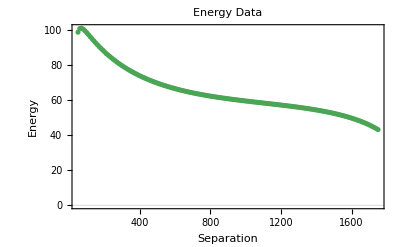

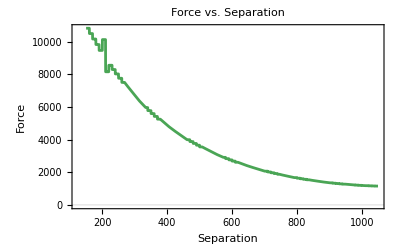

```mathematica
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}]
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]]
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

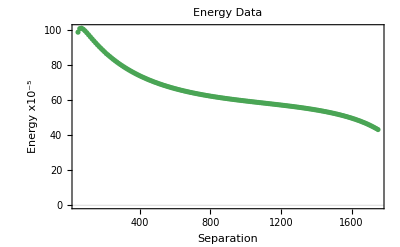

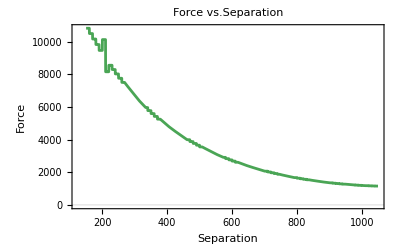

```mathematica
energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
```

```mathematica
Close[stream];
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None];
prettyData
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
|
```